```mathematica
λ = Eigenvalues[({{σ+1, 3}, {-2, σ-1}})]
```

{-ⅈ √5+σ,ⅈ √5+σ}

```mathematica
V = Eigenvectors[({{σ+1, 3}, {-2, σ-1}})]
```

{{1/2 (-1+ⅈ √5),1},{1/2 (-1-ⅈ √5),1}}

```mathematica
{{1/2 (-1+ⅈ √5),1},{1/2 (-1-ⅈ √5),1}}
```

```mathematica
{{A, B}}=Solve[C1*V[[1]]+C2*V[[2]]=={u, v}, {C1, C2}]
```

{{C1→-1/10 ⅈ (2 √5 u+5 ⅈ v+√5 v),C2→1/10 ⅈ (2 √5 u-5 ⅈ v+√5 v)}}

```mathematica
C1 = -1/10 ⅈ (2 √5 u+5 ⅈ v+√5 v)
```

-1/10 ⅈ (2 √5 u+5 ⅈ v+√5 v)

```mathematica
C2 = 1/10 ⅈ (2 √5 u-5 ⅈ v+√5 v)
```

1/10 ⅈ (2 √5 u-5 ⅈ v+√5 v)

```mathematica
S =C1*Exp[λ[[1]]*t]*V[[1]]+C2*Exp[λ[[2]]*t]*V[[2]]
```

{1/20 ⅈ (-1-ⅈ √5) ⅇ^(t (ⅈ √5+σ)) (2 √5 u-5 ⅈ v+√5 v)-1/20 ⅈ (-1+ⅈ √5) ⅇ^(t (-ⅈ √5+σ)) (2 √5 u+5 ⅈ v+√5 v),1/10 ⅈ ⅇ^(t (ⅈ √5+σ)) (2 √5 u-5 ⅈ v+√5 v)-1/10 ⅈ ⅇ^(t (-ⅈ √5+σ)) (2 √5 u+5 ⅈ v+√5 v)}

```mathematica
S = Simplify[ComplexExpand[S]]
```

{1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 (u+3 v) Sin[√5 t]),1/5 ⅇ^(t σ) (5 v Cos[√5 t]-√5 (2 u+v) Sin[√5 t])}

```mathematica
S/.{u-> 1, v-> 1, t->1, σ -> 0}
```

{1/5 (5 Cos[√5]+4 √5 Sin[√5]),1/5 (5 Cos[√5]-3 √5 Sin[√5])}

```mathematica
ParametricPlot[S/. {u -> 1, v -> 1, σ -> -1/10},{t, -10, 10}]/. Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]}
```

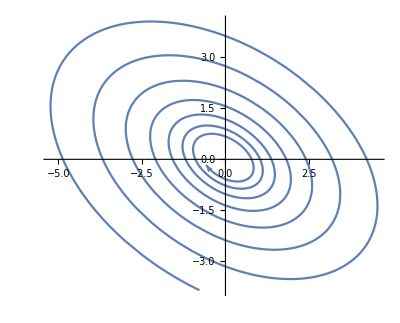

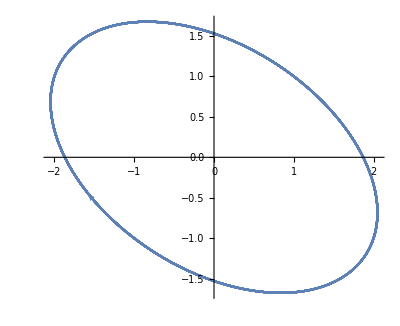

```mathematica
ParametricPlot[S/. {u -> 1, v -> 1, σ -> 0},{t, -10, 10}]/. Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]}
```

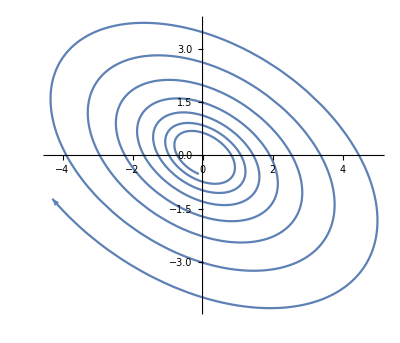

```mathematica
ParametricPlot[S/. {u -> 1, v -> 1, σ -> 1/10},{t, -10, 10}]/. Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]}
```

```mathematica
FunctionPeriod[S/. {u -> 1, v -> 1, σ -> 0},t]
```

(2 π)/(√5)

```mathematica
max =MaxValue[Norm[S]/. {u -> 1,v -> 1,σ -> 0},t]
```

MaxValue::ztest1: Unable to decide whether numeric quantity -10 Cos[2 ArcTan[Root[«1»&,2,0]]]^2+«5»+2 √5 Cos[2 ArcTan[Root[Plus[«5»]&,4,0]]] Sin[2 ArcTan[Root[Plus[«5»]&,4,0]]]+25 Sin[2 ArcTan[Root[«1»&,4,0]]]^2 is equal to zero. Assuming it is.

1/(√(5/(10 Cos[2 ArcTan[Root-1.16Root[1-14 #1+2 #1^2+14 #1^3+#1^4&,2]-1.1564851087973933]]^2+2 √5 Cos[2 ArcTan[Root-1.16Root[1-14 #1+2 #1^2+14 #1^3+#1^4&,2]-1.1564851087973933]] Sin[2 ArcTan[Root-1.16Root[1-14 #1+2 #1^2+14 #1^3+#1^4&,2]-1.1564851087973933]]+25 Sin[2 ArcTan[Root-1.16Root[1-14 #1+2 #1^2+14 #1^3+#1^4&,2]-1.1564851087973933]]^2)))

```mathematica
min = FindMinimum[Norm[S]/. {u -> 1,v -> 1,σ -> 0},t]
```

{1.39095,{t→1.34017}}

```mathematica
max[[1]]/min[[1]]
```

1.61803

```mathematica
dir = S/. {u -> 1,v -> 1,σ -> 0, max[[2]][[1]]}
```

{1.91448,-1.18322}

```mathematica
Normalize[dir]
```

{0.850651,-0.525731}